```mathematica
Clear[px1x2,py1y2,pz1z2,x1,x2,y1,y2,z1,z2]
px1x2[x1_,x2_]:=PDF[BinormalDistribution[{100,0.5},{10,0.05},-0.7],{x1,x2}]
py1y2[y1_,y2_]:=PDF[BinormalDistribution[{100,0.5},{15,0.1},0.5],{y1,y2}]
pz1z2[z1_,z2_]:=PDF[BinormalDistribution[{100,0.5},{5,0.02},0],{z1,z2}]
Plot3D[px1x2[x1,x2],{x1,50,150},{x2,0,1}, PlotRange->All]
Plot3D[py1y2[y1,y2],{y1,50,150},{y2,0,1}, PlotRange->All]
Plot3D[pz1z2[z1,z2],{z1,50,150},{z2,0,1}, PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

-Graphics3D-

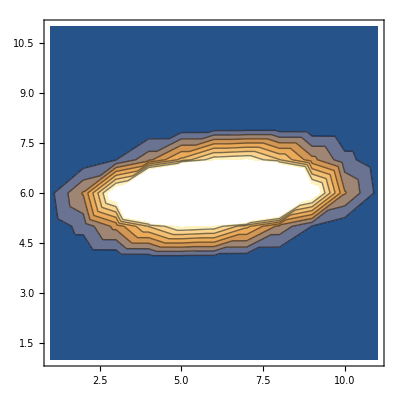

```mathematica
Clear[x1,x2,dx1,dx2,Pm,Pz1z2]
a=-50;b=50;p=11;
c=-1;d=1;q=11;
dx1=Range[a,b,(b-a)/(p-1)];
dx2=Range[c,d,(d-c)/(q-1)];
For[i=1,i< Length[dx1]+1,i++,
For [j=1,j<Length[dx2]+1,j++,
Pm[i,j]=NIntegrate[px1x2[x1,x2]py1y2[x1-dx1[[i]],x2-dx2[[j]]],{x1,-∞,∞},{x2,-∞,∞},MinRecursion->5, MaxRecursion->7]
]
]
Pz1z2=Table[Pm[i,j],{i,1,Length[dx1]},{j,1,Length[dx2]}];
pdx1dx2[dx1_,dx2_]:=Integrate[px1x2[x1,x2]py1y2[x1-dx1,x2-dx2],{x1,-∞,∞},{x2,-∞,∞}]
ListPlot3D[Transpose[Pz1z2],MeshStyle->Opacity[0.4],InterpolationOrder->1,ColorFunction->"SouthwestColors",DataRange->{{a,b},{c,d},Automatic},AxesLabel->{"dx1","dx2","P_dx1dx2"},PlotRange->All]
ListContourPlot[Transpose[Pz1z2]]
```

```mathematica
Clear[dz1,dz2,a,b,c,d,p,q]
(*pd2dintegrant[dz1_,dz2_,z1_,z2_]:=pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2*)
(*pd2dintegral[dz1_,dz2_]:=NIntegrate[pm2d[dz1*z1,dz2*z2]pz1z2[z1,z2]z1*z2,{z1,-500,500},{z2,-10,10},MinRecursion->5]*)
a=-1;b=1;p=11;
c=-1;d=1;q=11;
dz1=Range[a,b,(b-a)/(p-1)]
dz2=Range[c,d,(d-c)/(q-1)]
(*For[i=1,i< Length[dz1]+1,i++,
For [j=1,j<Length[dz2]+1,j++,
P[i,j]=NIntegrate[px1x2[x1,x2]py1y2[x1-dz1[[i]]*z1,x2-dz2[[j]]*z2]pz1z2[z1,z2]z1*z2,{x1,-200,200},{x2,-2,2},{z1,-200,200},{z2,-2,2},MinRecursion->9]
]
]*)
(*Plot3D[pd2dintegrant[0.1,0.1,z1,z2],{z1,-100,100},{z2,-10,10},PlotRange->All]*)
(*x=Array[pd2dintegral,{p,q},{{a,b},{c,d}}]*)
(*Clear[i,j,Pv1v2a,z1,z2]
Pv1v2a=Table[NIntegrate[pm2d[dz1[[i]]*z1,dz2[[j]]*z2]pz1z2[z1,z2]z1*z2,{z1,-200,200},{z2,-2,2},MinRecursion->9,MaxRecursion->12],{i,1,Length[dz1]},{j,1,Length[dz2]}]*)
Clear[i,j, Pv1v2b,z1,z2]
Pv1v2b=Table[NIntegrate[px1x2[x1,x2]py1y2[x1-dz1[[i]]*z1,x2-dz2[[j]]*z2]pz1z2[z1,z2]z1*z2,{x1,-1000,1000},{x2,-10,10},{z1,-1000,1000},{z2,-10,10},MinRecursion->4,MaxRecursion->6],{i,1,Length[dz1]},{j,1,Length[dz2]}]
ListPlot3D[Transpose[Pv1v2b],MeshStyle->Opacity[0.4],InterpolationOrder->1,ColorFunction->"SouthwestColors",DataRange->{{a,b},{c,d},Automatic},AxesLabel->{"v1","v2","P_v1v2"},PlotRange->All]
ListContourPlot[Transpose[Pv1v2b],DataRange->{{a,b},{c,d},Automatic}]
```

{-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1}

{-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.01527×10^-75 and 2.01527×10^-75 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.58187×10^-68 and 5.58187×10^-68 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.30936×10^-62 and 7.30936×10^-62 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

$Aborted

ListPlot3D::arrayerr: Transpose[Pv1v2b] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[Pv1v2b],MeshStyle→Opacity[0.4],InterpolationOrder→1,ColorFunction→SouthwestColors,DataRange→{{-1,1},{-1,1},Automatic},AxesLabel→{v1,v2,P_v1v2},PlotRange→All]

ListContourPlot::arrayerr: Transpose[Pv1v2b] must be a valid array.

ListContourPlot[Transpose[Pv1v2b],DataRange→{{-1,1},{-1,1},Automatic}]